## Hydrogen Atom using Numerov Method

Due to (⟨r⟩~n^2, we need a variable mesh grid.  We then need a corresponding rescaling of the wavefunction to preserve the Numerov form.  Let ψ(r)=J(s(r))χ(s(r)).  We want to choose J so that first derivatives are eliminated in the Schrodinger equation.

One choice of mesh is r=s^2

```mathematica
D[(J[√r]χ[√r]), r,r]/.{r->s^2}//PowerExpand
```

-(χ[s] J'[s])/(4 s^3)-(J[s] χ'[s])/(4 s^3)+(J'[s] χ'[s])/(2 s^2)+(χ[s] J''[s])/(4 s^2)+(J[s] χ''[s])/(4 s^2)

```mathematica
Collect[%,χ'[s]]
```

-(χ[s] J'[s])/(4 s^3)+(-J[s]/(4 s^3)+J'[s]/(2 s^2)) χ'[s]+(χ[s] J''[s])/(4 s^2)+(J[s] χ''[s])/(4 s^2)

To eliminate the first derivative we need 2 J[s]+8 s J'[s]=0

```mathematica
DSolve[-J[s]/(4 s^3)+J'[s]/(2 s^2)==0,J[s],s]
```

{{J[s]→√s C[1]}}

To get in eigenvalue form, multiply SE by 1/√s

```mathematica
SE=1/(√s)(-1/2 D[(r^(1/4)χ[√r]), r,r]-(ℰ-V[r])r^(1/4)χ[√r]/.{r->s^2})//PowerExpand//Simplify//Expand
```

(3 χ[s])/(32 s^4)-ℰ χ[s]+V[s^2] χ[s]-χ''[s]/(8 s^2)

```mathematica
V[r_]:=-1/r;ϵm=20.;
(*determine grid, rmax=4000*)
n=500;ds=√4000./n;
s=Table[-ds /2+ds i,{i,n}];
(*calculate KE matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=(one[n,-1]+10 one[n,0]+one[n,1])/12.;
A=(one[n,-1]-2 one[n,0]+one[n,1])/ds^2;
KE=-DiagonalMatrix[1/(8 s^2)].Inverse[B].A;
(*Hamiltonian*)
H=KE+DiagonalMatrix[V[s^2]+3/(32 s^4)];
(*Energies, wavefunctions*)
{eval,evec}=Eigensystem[H];in=Ordering[eval];eval=eval⟦in⟧;evec=evec⟦in⟧;
```

calculate effective quantum number from the energies, accurate out to about n=40

```mathematica
√(-1/(2eval⟦;;50⟧))
```

{0.999228,1.99921,2.99919,3.99917,4.99915,5.99913,6.99911,7.99909,8.99907,9.99904,10.999,11.999,12.999,13.999,14.9989,15.9989,16.9989,17.9989,18.9989,19.9988,20.9988,21.9988,22.9988,23.9987,24.9987,25.9987,26.9987,27.9987,28.9986,29.9986,30.9986,31.9986,32.9986,33.9985,34.9985,35.9985,36.9985,37.9984,38.9984,39.9984,40.9984,41.999,43.0079,44.067,45.2695,46.7071,48.4457,50.5564,53.142,56.3615}

Here is the n=40 wavefunction as a function of r

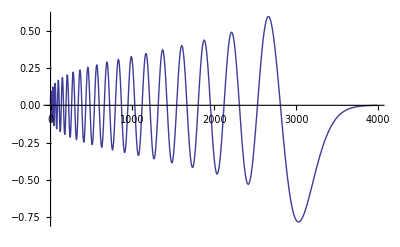

```mathematica
ListPlot[{s^2,s^(1/2)evec⟦40⟧}ᵀ,PlotRange->All,Joined->True]
```

Plotted vs s, the nonlinear grid has smoothed out the wavefunction to be closer to a sine wave

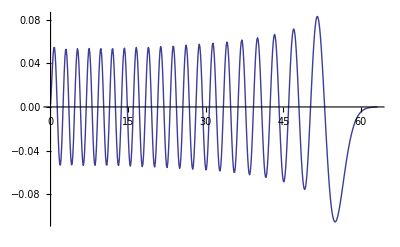

```mathematica
ListPlot[{s,evec⟦40⟧}ᵀ,PlotRange->All,Joined->True]
```

1s wavefunction still pretty accurate

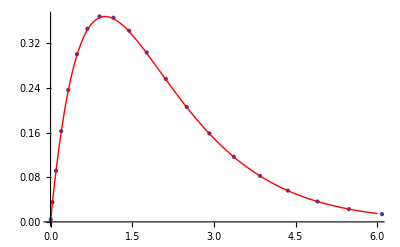

```mathematica
Show[ListPlot[{s^2,s^(1/2)evec⟦1⟧}ᵀ,PlotRange->{{0,6},All},Joined->False],Plot[x Exp[-x],{x,0,6},PlotStyle->Red]]
```